Comparison between the two bases for polynomials

9

{1,p,p^2,p^3,p^4,p^5,p^6,p^7,p^8,p^9}

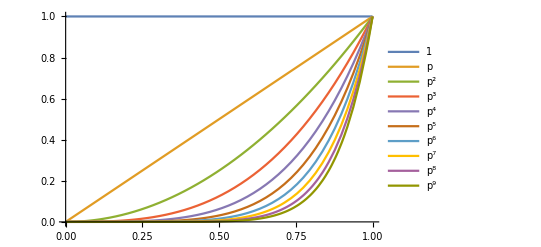

{(1-p)^9,(1-p)^8 p,(1-p)^7 p^2,(1-p)^6 p^3,(1-p)^5 p^4,(1-p)^4 p^5,(1-p)^3 p^6,(1-p)^2 p^7,(1-p) p^8,p^9}

{(1-p)^9,9 (1-p)^8 p,36 (1-p)^7 p^2,84 (1-p)^6 p^3,126 (1-p)^5 p^4,126 (1-p)^4 p^5,84 (1-p)^3 p^6,36 (1-p)^2 p^7,9 (1-p) p^8,p^9}

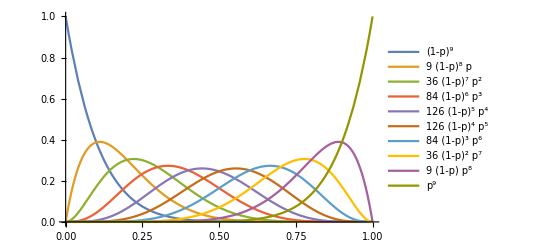

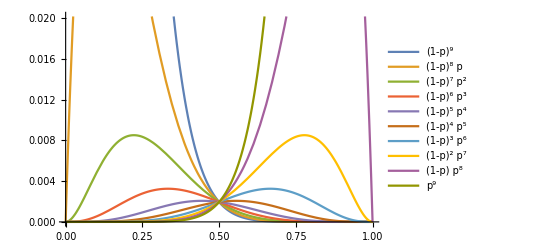

```mathematica
n = 9
pbase = Table[p^i,{i,0,n}]
Plot[pbase,{p,0,1}, PlotLegends->"Expressions"]
basef[i_,m_,p_]=p^i(1-p)^(m-i);
base = Table[basef[i,n,p],{i,0,n}]
basescale = Table[Binomial[n,i]*basef[i,n,p],{i,0,n}]
Plot[basescale,{p,0,1},PlotLegends->"Expressions",PlotRange->All]
Plot[base,{p,0,1},PlotLegends->"Expressions"]
```